3.80919

0.0305789

2mer.png

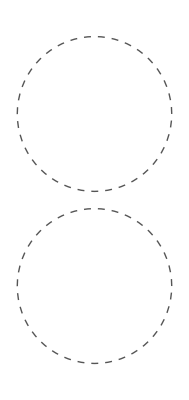

```mathematica
ClearAll["Global`*"]
Subscript[m, e]=9.10938291*10^(-31); (*Kg*) ch=1.602176565*10^(-19); (*C*) ℏ=1.054571726*10^(-34); (*J·s*)
Subscript[ℏ, eV]=6.58211928*10^(−16);(*eV·s*) c=2.99*10^(8); (*m^2·s^-2*) ev=1.602176565*10^(-19); (*J*)
Subscript[m, e,eV]=Subscript[m, e]*c^2/ev; (*MeV·c^2*) ϵ0=8.85418782*10^(-12); (*C^2·N^-1·m^-2*) nm=10^(-9); (*m*)
(*Metal parameters*)
ϵd=1; ϵinf=3.77; (*no dimensions, Relative permittivity*) a0=7*nm; ℏωp=9.15; (*eV*)  ωp=ℏωp/Subscript[ℏ, eV];
 ωsp=ωp/Sqrt[ϵinf+2*ϵd]; αsp=4*π*ϵ0*a0^3*(3/(ϵinf+2));
m=ch^2/(αsp*ωsp^2); ℏωsp=ℏ*ωsp/ch
(*Geometry*)
d0=4*nm; r0=(2+d0/a0)//N; (*Coupling*) g0=αsp/(4*π*ϵ0*a0^3*r0^3)
e2=Sqrt[3]/2;  e1=(1/2); r={x,y,z} ; id={{1,0,0},{0,1,0},{0,0,1}};
Rloc[n_]:=r-Loc[[n]];


numPart = 2;

(*Loc={{0,e1,0},{0,-e1,0},{-e2,2*e1,0},{-2*e2,e1,0},{-2*e2,-e1,0},{-e2,-2*e1,0},{e2,-2*e1,0},{2*e2,-e1 ,0},{2*e2 ,e1 ,0},{e2 ,2*e1 ,0}(*,{0,6*e1,0}*)};*)

Loc={{0,e1,0},{0,-e1,0}};

Loc2D=Table[Delete[Loc[[j]],3],{j,1,numPart}];

Pnts=Point[Loc2D];

Crcs=Table[Graphics[{Thick,Dashed,Darker[Gray],Circle[Flatten[Loc2D[[j]]],0.45]}],{j,1,numPart}];
Crcs2=Table[Graphics[{Thickness[0.008],Black,Circle[Flatten[Loc2D[[j]]],0.45]}],{j,1,numPart}];
G1=Graphics[{Opacity[0.2],PointSize[0.17],Yellow,Pnts}];
G2=Show[Crcs];
G3=Graphics[Line[Join[Loc2D,{Loc2D[[1]]}]]];
G4=Graphics[Line[{Loc2D[[1]],Loc2D[[numPart]]}]];
Export["2mer.png",G2]
Gfin=Show[Crcs]
```

True

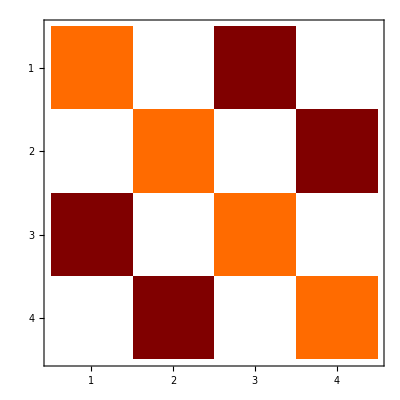

(1 | 0 | g | 0
0 | 1 | 0 | -2 g
g | 0 | 1 | 0
0 | -2 g | 0 | 1)

```mathematica
FullM0=IdentityMatrix[2*numPart];
R[n_,m_]:=(Rloc[n]-Rloc[m]);
NormR[n_,m_]:=Norm[R[n,m]];
nUnit[n_,m_]:=R[n,m]/NormR[n,m];

T1[n_,m_]:=id/NormR[n,m]^(3);

T2[n_,m_]:=-3*Outer[Times,nUnit[n,m],nUnit[n,m]]/NormR[n,m]^(3);

Coupling[n_,m_]:=(g)*(T1[n,m]+T2[n,m])[[1;;2,1;;2]];


F1=Do[If[n≠m  && Norm[R[n,m]]>=1 ,FullM0[[2*n-1;;2*n,2*m-1;;2*m]]=Coupling[n,m]],{n,1,numPart},{m,1,numPart}];


F3=FullM0;
F2=FullM0;
SymmetricMatrixQ[F2]
MatrixPlot[F2]
F2
```

```mathematica
g=g0;
EigSys2=Eigensystem[F2];
Table[ Sqrt[EigSys2[[1]][[m]]],{m,1,2*numPart}]
Table[ Sqrt[EigSys2[[1]][[m]]],{m,1,2*numPart}];
```

{1.03013,1.01517,0.984592,0.968939}

```mathematica
p[j_,n_]:={EigSys2[[2]][[j]][[2*n-1]],EigSys2[[2]][[j]][[2*n]],0};
pd[j_]:=Table[p[j,k]/Norm[p[j,k]],{k,1,numPart}];
Ph[j_,k1_]:=pd[j][[k1]].Rloc[k1]/((Rloc[k1][[1]])^2+(Rloc[k1][[2]])^2+(Rloc[k1][[3]])^2)^(3/2);
Phtot[j_]:=Table[Ph[j,n],{n,1,numPart}];
Potentials=Table[Total[Phtot[j]]/.z->0,{j,1,2*numPart}];
Dipoles=Table[Table[Graphics[{Thickness[0.01],Arrowheads[0.08],Black,Arrow[{{Loc[[n]][[1]],Loc[[n]][[2]]},{(Loc[[n]][[1]]+p[j,n][[1]]),(Loc[[n]][[2]]+p[j,n][[2]])}}]}],{n,1,numPart}],{j,1,2*numPart}];
Dipoles2=Table[Table[Graphics[{Thickness[0.01],Arrowheads[0.12],Black,Arrow[{{Loc[[n]][[1]],Loc[[n]][[2]]},{(Loc[[n]][[1]]-p[j,n][[1]]),(Loc[[n]][[2]]-p[j,n][[2]])}}]}],{n,1,numPart}],{j,1,2*numPart}];
Dipoles3=Table[Table[Graphics[{Thickness[0.01],Arrowheads[0.12],Black,Arrow[{{Loc[[n]][[1]],Loc[[n]][[2]]},{(Loc[[n]][[1]]+p[j,n][[1]]),(Loc[[n]][[2]]+p[j,n][[2]])}}]}],{n,1,numPart}],{j,1,2*numPart}];

ColorData["Gradients"];
(*BFields[k_]:=Total[Table[(3*Rloc[j]*(Cross[Rloc[j],p[k,j]].Rloc[j]))*(1/(Rloc[j][[1]]^2+Rloc[j][[2]]^2+Rloc[j][[3]]^2)^(5/2))-(Cross[Rloc[j],p[k,j]])*(1/(Rloc[j][[1]]^2+Rloc[j][[2]]^2+Rloc[j][[3]]^2)^(3/2)),{j,1,numPart}]];
Bf=Table[BFields[j][[3]]/.z->0.0,{j,1,2*numPart}];*)
M[k_,j_]:=Cross[Rloc[j],p[k,j]];
M2[k_,n_]:=Cross[Loc[[n]],p[k,n]];
BFields[k_]:=Total[Table[3*Rloc[j]*(M[k,j].Rloc[j])/Norm[Rloc[j]]^3-M[k,j]/Norm[Rloc[j]]^3,{j,1,numPart}]];
Bf=Table[BFields[k]/.z->0,{k,1,2*numPart}];
```

```mathematica
map=Import["/Users/cherqui/Documents/colormap.dat","Table"];
MB=Function[Blend[RGBColor@@@ map,#1]];

(*TwomerPlots=Table[Show[ContourPlot[-Bf[[j]][[3]],{x,-2.5,2.5},{y,-1.5,1.5},ContourStyle->None,Contours->201,PlotPoints->100,ImageSize->Large,ColorFunction->MB, PlotLegends->None,PlotRange->{-0.5,0.5},AspectRatio->Automatic,ContourShading->Automatic,ClippingStyle->Automatic,FrameTicks->None,Frame->False(*,PlotLabel->ℏωsp*Sqrt[EigSys2[[1]][[j]]]*)],Gfin,Dipoles2[[j]]],{j,1,2*numPart}]*)
```

```mathematica
PicsTwomer=Table[Export[FileNameJoin[StringJoin["2mer_ModeNN[", ToString[j],"].png"]],TwomerPlots[[j]]],{j,1,1}]
```

Part::partd: Part specification TwomerPlots⟦1⟧ is longer than depth of object.

{2mer_ModeNN[1].png}